```mathematica
SetDirectory[NotebookDirectory[]];
points = Import["project\\project\\in.txt", "Table"][[2;;]];
polygon =Import["project\\project\\out.txt", "Table"][[2;;]]
```

{{-1.87938,-0.101262},{-0.783653,0.95143},{1.02205,0.869363},{1.8307,0.288838},{1.91843,0.102253},{1.65012,-0.994884},{-1.72664,-0.925785},{-1.87938,-0.101262}}

```mathematica
ListPlot[points,PlotStyle->Red, PlotRange->All];
```

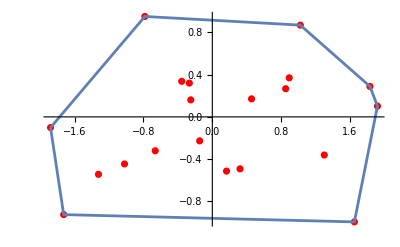

```mathematica
Show[ListPlot[points,PlotStyle->Red], ListLinePlot[polygon], PlotRange->All]
```

```mathematica
points2 = Import["task2\\task2\\in.txt", "Table"][[2;;]]
polygon2 =Import["task2\\task2\\out.txt", "Table"][[2;;]]
```

{{0,0},{1,0},{0,1},{1,1},{0.5,0.5},{0.6,1.5}}

{{1,0},{1,1},{0,1},{0,0},{1,0}}

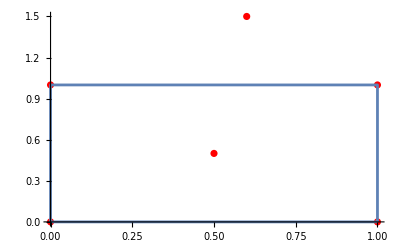

```mathematica
Show[ListPlot[points2,PlotStyle->Red], ListLinePlot[polygon2], PlotRange->All]
```